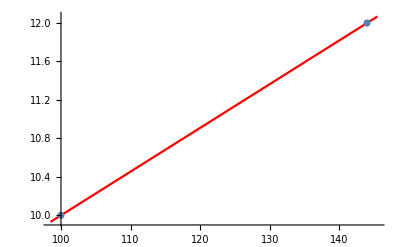

L(t) = 5.45+0.0455 t

L(121.) = 10.9545,  точна стойност = 11.

M_(n + 1)=0.00025

R = 0.060375

```mathematica
(* Задача 1 *)
Clear[f,xx,n,yy];
u=121.;(* точката, в която търсим приближена ст-ст *)
f[t_]:=√t
xx={100,144};
n=Length[xx];
yy=Table[f[xx[[i]]],{i,1,n}];
sp=Table[{xx[[i]],yy[[i]]},{i,1,n}];
g1=ListPlot[sp];
(*Print[{xx,yy}//TableForm];*)
L[t_]:=∑_(i=1)^n yy[[i]]∏_(j=1)^n If[i≠j,(t-xx[[j]])/(xx[[i]]-xx[[j]]),1];
g2=Plot[L[t],{t,xx[[1]]-1.5,xx[[n]]+1.5},PlotStyle->{Red}];
Show[g2,g1]
Print["L(t) = ",N[Collect[L[t],t],3]]
Print["L(",u,") = ",L[u],",  точна стойност = ",f[u]];
ff=D[f[t],{t,n}];
M=Maximize[{Abs[ff],xx[[1]]≤t≤xx[[n]]},t][[1]];
Print["M_(n + 1)=",M//N];
 R=M/(n!)*∏_(i=1)^n Abs[(u-xx[[i]])];  Print["R = ",Abs[R]]
```

1. | 1.1 | 1.3
1. | 1.03228 | 1.09139

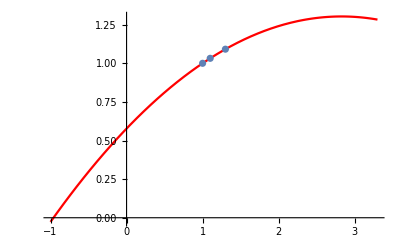

L(1.15) = 1.04774,  точна стойност = 1.04769

L(t)=0.577329+0.513462 t-0.0907911 t^2

M_(n + 1)=0.37037

R=0.0000173611

```mathematica
(* Задача 4 *)
f[t_]:=t^(1/3)
u=1.15 ;(* точката, в която търсим приближена ст-ст *)
xx={1.,1.1,1.3};
n=Length[xx];
yy=Table[f[xx[[i]]],{i,1,n}];
sp=Table[{xx[[i]],yy[[i]]},{i,1,n}];
g1=ListPlot[sp];
Print[{xx,yy}//TableForm]
L[t_]:=∑_(i=1)^n yy[[i]]∏_(j=1)^n If[i≠j,(t-xx[[j]])/(xx[[i]]-xx[[j]]),1]
g2=Plot[L[t],{t,xx[[1]]-2,xx[[n]]+2},PlotStyle->{Red}];
Show[g2,g1]
Print["  L(",u,") = ",L[u],",  точна стойност = ",f[u]];
Print["  L(t)=",Collect[L[t],t]]
 ff=D[f[t],{t,n}];
M=Maximize[{Abs[ff],xx[[1]]≤t≤xx[[n]]},t][[1]];
Print["  M_(n + 1)=",M];
 R=M/((n+1)!)*∏_(i=1)^n (u-xx[[i]]);  Print["  R=",Abs[R]]
```

-2 | -1 | 0 | 1
1/7 | 1/4 | 1/3 | 1/4

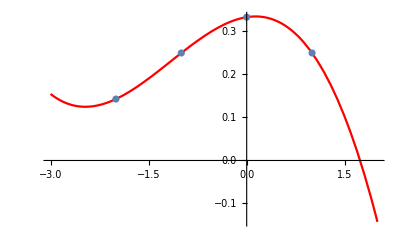

L(t) = 0.333+0.0238 t-0.0833 t^2-0.0238 t^3

L(0.5) = 0.321429,  точна стойност = 0.307692

M_(n + 1)=0.888889

R = 0.0347222

```mathematica
(* Задача 5 *)
f[t_]:=1/(t^2+3)
(*n=(b-a)/h; h=(b-a)/n*)
a=-2.;b=1.;(* interval za x *)
u=0.5 ;
h=1; 
xx={-2,-1,0,1};
n=Length[xx];
yy=Table[f[xx[[i]]],{i,1,n}];
sp=Table[{xx[[i]],yy[[i]]},{i,1,n}];
g1=ListPlot[sp];
Print[{xx,yy}//TableForm]
L[t_]:=∑_(i=1)^n yy[[i]]∏_(j=1)^n If[i≠j,(t-xx[[j]])/(xx[[i]]-xx[[j]]),1]
g2=Plot[L[t],{t,xx[[1]]-1,xx[[n]]+1},PlotStyle->{Red}];
Show[g2,g1]
Print["L(t) = ",N[Collect[L[t],t],3]]
Print["L(",u,") = ",L[u],",  точна стойност = ",f[u]];
ff=D[f[t],{t,n}];
M=Maximize[{Abs[ff],xx[[1]]≤t≤xx[[n]]},t][[1]];
Print["M_(n + 1)=",M//N];
 R=M/(n!)*∏_(i=1)^n Abs[(u-xx[[i]])];  Print["R = ",Abs[R]]
```

1.2 | 1.4 | 1.6
2.04939 | 2.09762 | 2.14476

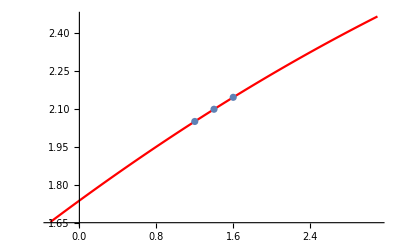

L(t) = 1.73726+0.276374 t-0.0135523 t^2

L(1.49) = 2.11897,  точна стойност = 2.11896

M_(n + 1)=0.0103731

R = 4.96352×10^-6

```mathematica
(* Задача 2.1, стр. 91, Учебник по ПМ2, u = 1.49 чрез Лагранж от втора и трета степен и да се оцени грешката *)
Clear[f,xx,n,yy];
u=1.49;(* точката, в която търсим приближена ст-ст *)
f[t_]:=√(t+3)
xx=Table[k,{k,1.2,1.6,0.2}];
n=Length[xx];
yy=Table[f[xx[[i]]],{i,1,n}];
sp=Table[{xx[[i]],yy[[i]]},{i,1,n}];
g1=ListPlot[sp];
Print[{xx,yy}//TableForm];
L[t_]:=∑_(i=1)^n yy[[i]]∏_(j=1)^n If[i≠j,(t-xx[[j]])/(xx[[i]]-xx[[j]]),1]
g2=Plot[L[t],{t,xx[[1]]-1.5,xx[[n]]+1.5},PlotStyle->{Red}];
Show[g2,g1]
Print["L(t) = ",N[Collect[L[t],t],3]]
Print["L(",u,") = ",L[u],",  точна стойност = ",f[u]];
ff=D[f[t],{t,n}];
M=Maximize[{Abs[ff],xx[[1]]≤t≤xx[[n]]},t][[1]];
Print["M_(n + 1)=",M//N];
 R=M/(n!)*∏_(i=1)^n Abs[(u-xx[[i]])];  Print["R = ",Abs[R]]
```

{1.2,1.4,1.6,1.8}

1.2 | 1.4 | 1.6 | 1.8
2.04939 | 2.09762 | 2.14476 | 2.19089

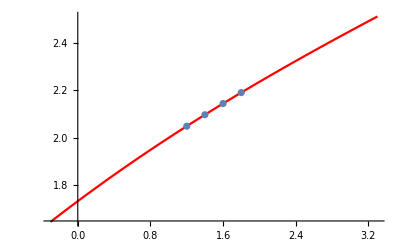

L(t) = 1.73334+0.284889 t-0.0196763 t^2+0.0014581 t^3

L(1.49) = 2.11896,  точна стойност = 2.11896

M_(n + 1)=0.00617446

R = 2.28972×10^-7

```mathematica
(* Задача 2.1, стр. 91, Учебник по ПМ2, u = 1.49 чрез Лагранж от втора и трета степен и да се оцени грешката *)
Clear[f,xx,n,yy];
u=1.49;(* точката, в която търсим приближена ст-ст *)
f[t_]:=√(t+3)
xx=Table[k,{k,1.2,1.8,0.2}]
n=Length[xx];
yy=Table[f[xx[[i]]],{i,1,n}];
sp=Table[{xx[[i]],yy[[i]]},{i,1,n}];
g1=ListPlot[sp];
Print[{xx,yy}//TableForm];
L[t_]:=∑_(i=1)^n yy[[i]]∏_(j=1)^n If[i≠j,(t-xx[[j]])/(xx[[i]]-xx[[j]]),1]
g2=Plot[L[t],{t,xx[[1]]-1.5,xx[[n]]+1.5},PlotStyle->{Red}];
Show[g2,g1]
Print["L(t) = ",N[Collect[L[t],t],3]]
Print["L(",u,") = ",L[u],",  точна стойност = ",f[u]];
ff=D[f[t],{t,n}];
M=Maximize[{Abs[ff],xx[[1]]≤t≤xx[[n]]},t][[1]];
Print["M_(n + 1)=",M//N];
 R=M/(n!)*∏_(i=1)^n Abs[(u-xx[[i]])];  Print["R = ",Abs[R]]
```